#### Polytropic interpolation for G2 EoS

```mathematica
(**latdat=Import["/Users/yannickdengler/Documents/Uni/PhD_Graz/Code/G2_stars/EoS/data/EoS_G2_prime"]**)
latdat=Import[NotebookDirectory[]<>"input/EoS_G2_prime"]
```

{{0.,1.67298×10^-6,1.67298×10^-6},{0.,0.0000312307,0.0000312307},{0.0368098,8.78773×10^-6,8.78773×10^-6},{0.0736196,-7.20746×10^-6,-7.20746×10^-6},{0.110429,0.000038993,0.000038993},{0.147239,1.64323×10^-7,1.64323×10^-7},{0.184049,0.0000564298,0.0000564298},{0.220859,0.00013196,0.00013196},{0.257669,0.000141566,0.0000259196},{0.294479,0.000190949,0.000190949},{0.331288,0.00015508,0.00015508},{0.368098,0.000301304,0.000301304},{0.404908,0.000292064,0.000292064},{0.441718,0.00033533,0.00033533},{0.478528,0.000356087,0.000356087},{0.515337,0.000470092,0.000470092},{0.552147,0.000747099,0.000747099},{0.588957,0.000821352,0.000821352},{0.625767,0.000971272,0.000971272},{0.662577,0.000921666,0.000921666},{0.699387,0.00142987,0.0000885475},{0.736196,0.00185749,0.00185749},{0.773006,0.0019786,0.0000408614},{0.809816,0.00211767,0.00211767},{0.846626,0.0021546,0.0000397255},{0.883436,0.0022343,0.0022343},{0.920245,0.00245097,0.0000758474},{0.957055,0.00254334,0.00254334},{0.993865,0.00296142,0.0000708534},{1.03068,0.00346021,0.00346021},{1.06749,0.00389707,0.0000748133},{1.10429,0.00451893,0.00451893},{1.1411,0.0050182,0.00013126},{1.17791,0.00613572,0.0000188598},{1.25153,0.0070371,0.0000263293},{1.32515,0.0101906,0.0000549543},{1.39877,0.0119938,0.000648161},{3.68098,1.07757,0.}}

```mathematica
Length[latdat]
nsat = latdat[[38,2]]
μsat = latdat[[38,1]]
μgt1=latdat[[30;;37]];
Length[%]
```

38

1.07757

3.68098

8

```mathematica
μPP[n_, c_, Γ_, K_]:=c+Γ*K*n^(Γ-1)/(Γ-1)
PPP[n_, Γ_, K_]:=K*n^Γ
epsPP[n_,c_,Γ_,K_]:=c*n+K*n^Γ/(Γ-1)
csPP[n_,c_,Γ_,K_]:=(Γ*PPP[n, Γ, K])/(PPP[n, Γ, K]+epsPP[n,c, Γ, K])
```

```mathematica
nFD[μ_, a_,b_]:=nsat/(Exp[a-b*μ]+1)
μFD[n_,a_,b_]:=(a-Log[nsat/n-1])/b
```

```mathematica
n1=latdat[[35,2]];
n2=latdat[[37,2]];
μ1=latdat[[35,1]];
μ2=latdat[[37,1]];
a=(μ1 Log[(n1 (n2-nsat))/(n2 (n1-nsat))])/(μ1-μ2)+Log[-1+nsat/n1];
b=Log[(n1 (n2-nsat))/(n2 (n1-nsat))]/(μ1-μ2);
μarrFD = Table[x,{x,1.5,3.5,0.5}];
narrFD = Table[nFD[μarrFD[[i]],a,b],{i,Length[μarrFD]}];
```

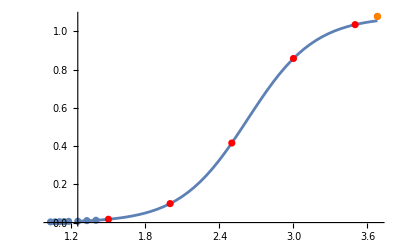

```mathematica
Plotlist={};
AppendTo[Plotlist,Plot[nFD[μ,a,b],{μ,μ1,μsat}]];
AppendTo[Plotlist,ListPlot[Transpose@{μgt1[[All,1]],μgt1[[All,2]]}]];
AppendTo[Plotlist,ListPlot[{{μsat,nsat}},PlotStyle->Orange]];
AppendTo[Plotlist,ListPlot[Transpose@{μarrFD,narrFD},PlotStyle->Red]];
Show[Plotlist, PlotRange->All]
```

```mathematica
(**nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=NSolve[0==(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,Γ]**)
nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=Γ/.FindRoot[(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,{Γ,1.5},PrecisionGoal->6]
nextK[n0_,Γ1_,P0_]:=n0^-Γ1 P0
nextc[μ1_,n1_,K1_,Γ1_]:=μ1-(K1 n1^(-1+Γ1) Γ1)/(Γ1-1)
nextP[n1_,Γ1_,K1_]:=K1 n1^Γ1
```

```mathematica
narr = Join[μgt1[[All,2]],narrFD];
μarr = Join[μgt1[[All,1]],μarrFD];
Length[μarr]
Length[μgt1[[All,1]]]
```

13

8

```mathematica
Γ00=5/3//N;
c00=1;
Γarr = Table[0,{i,Length[narr]}];
carr = Table[0,{i,Length[narr]}];
Karr = Table[0,{i,Length[narr]}];
Parr = Table[0,{i,Length[narr]}];
epsarr = Table[0,{i,Length[narr]}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
epsarr[[1]]=epsPP[narr[[1]],carr[[1]],Γarr[[1]],Karr[[1]]];
```

```mathematica
For[i=2,i<Length[narr]+1,i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
epsarr[[i]]=epsPP[narr[[i]],carr[[i]],Γarr[[i]],Karr[[i]]];
]
```

```mathematica
μarr
narr;
Parr;
carr
Karr
Γarr
Parr
Export[NotebookDirectory[]<>"output/cKgP_DM_light.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{1.03068,1.06749,1.10429,1.1411,1.17791,1.25153,1.32515,1.39877,1.5,2.,2.5,3.,3.5}

{1,1.0173,1.00712,1.00568,0.889334,1.0193,-0.184191,1.00369,0.125906,-1.12189,-0.591396,1.61393,2.28278}

{0.536344,2.88518×10^25,2.57787×10^6,928795.,3.70119,166024.,0.333626,59.6124,0.558216,0.357475,0.376984,0.582041,0.815693}

{1.66667,12.1225,4.21596,4.0269,1.6787,3.78157,1.13505,2.26572,1.20977,1.09996,1.12294,1.61801,3.81907}

{0.0000424568,0.000179435,0.00033495,0.000510806,0.000715873,0.00120211,0.00183007,0.00264716,0.00411567,0.0280925,0.140755,0.454158,0.929846}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/cKgP_DM_light.csv

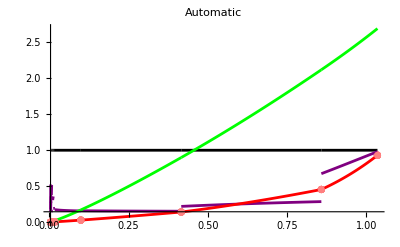

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];
AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
AppendTo[Plotlist,ListPlot[Transpose@{narr,Parr},PlotStyle->Pink]];
]
Show[Plotlist,PlotRange->Automatic,PlotLabel->Automatic]
```

```mathematica
convmN4=101425.86;
```

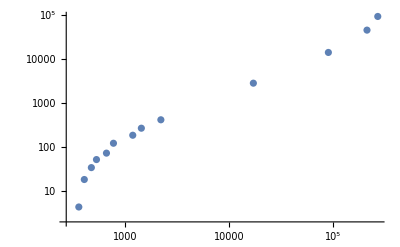

```mathematica
ListLogLogPlot[Table[{epsarr[[i]]*convmN4,Parr[[i]]*convmN4},{i,1,Length[Parr]}]]
```

```mathematica
epsarrout=epsarr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Parrout=Parr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Export[NotebookDirectory[]<>"output/light_points.dat",{epsarrout,Parrout}]
```

{357.414,403.739,472.165,528.985,660.433,771.35,1184.05,1433.09,2210.55}

{4.30621,18.1993,33.9726,51.8089,72.608,121.925,185.617,268.49,417.436}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/light_points.dat